```mathematica
ClearAll[Dim];
Dim[𝓉0_,𝓉e_,α_,𝓀_,ϕ1_,time_]:=
(
{𝒩,𝒜,ℳ}=
{200,1.22,(931.4943 13)/9};
ϕ=ϕ1;
{elecT,kineT,potT,chaT,c,e}=Array[{}&,6];
𝓋=Array[0&,{𝒩}];
Φ={};
{ℯ,𝒸}={2,0};
(*hamiltonian*)
ls=-Array[𝓉0+α (-1)^(#+1) (ϕ[[#+1]]+ϕ[[#]])+(-1)^(#+1) 𝓉e&,199];
ls=Append[ls,0];
ls2=DiagonalMatrix[ls];
ℋ=RotateRight[ls2]+Transpose@RotateRight[ls2];

(*eigen problem*)
{ℰ,𝒵}=Transpose@Sort[Transpose[Eigensystem[ℋ]], #1[[1]] < #2[[1]] &];

For[t=1,t≤ time,t++,
(*start*)

(*hamiltonian*)
ls=-Array[𝓉0+α (-1)^(#+1) (ϕ[[#+1]]+ϕ[[#]])+(-1)^(#+1) 𝓉e&,199];
ls=Append[ls,0];
ls2=DiagonalMatrix[ls];
ℋ=RotateRight[ls2]+Transpose@RotateRight[ls2];

(*eigen problem*)
{ℰ,𝒵}=Transpose@Sort[Transpose[Eigensystem[ℋ]], #1[[1]] < #2[[1]] &];

(*bcd*)
𝓅=Array[2&,𝒩/2-1]~Join~{ℯ,𝒸};
{w1,w2,it}=
{Transpose[𝒵]⟦1;;199,1;;101⟧,Transpose[𝒵]⟦2;;200,1;;101⟧,
Array[𝓅&,199]};
r𝒲=Apply[Plus,w1 it w2,{1}];
𝒦=(Plus@@r𝒲)(2α)/200;

(*fh*)
ℱ=Insert[(Rest@r𝒲-Most@r𝒲)Riffle[Array[-1&,198/2],Array[1&,198/2]] 2 α-(ϕ⟦3;;200⟧+2ϕ⟦2;;199⟧+ϕ⟦1;;198⟧) 𝓀,0,{{1},{-1}}]+{2 α r𝒲⟦1⟧-𝓀(ϕ⟦1⟧+ϕ⟦2⟧)-𝒦}~Join~Array[0&,198,2]~Join~{2 α r𝒲⟦199⟧-𝓀(ϕ⟦199⟧+ϕ⟦200⟧)-𝒦};

(*classical motion*)
𝓋=0.98 𝓋+ℱ/ℳ;
ϕ=ϕ+𝓋 0.98;

ϕ[[2;;199]]=(ϕ[[1;;198]]+ϕ[[2;;199]]+ϕ[[3;;200]])/3;
Φ=Append[Φ,ϕ];

]//AbsoluteTiming
)
```

```mathematica
ϕ1=Flatten@Import["phi.dat"];
```

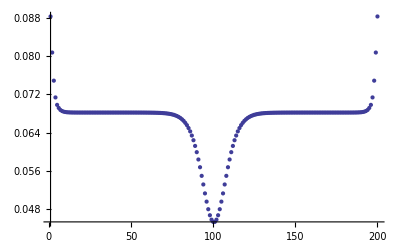

```mathematica
ListPlot[ϕ1,PlotRange->All]
```

```mathematica
{𝓉0,𝓉e,α,𝓀}={4.0,0.09,5.0,19.9};
```

```mathematica
Dim[𝓉0,𝓉e,α,𝓀,ϕ1,1000]
```

{40.64532,Null}

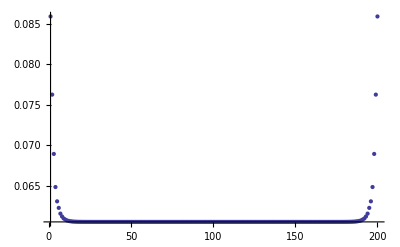

```mathematica
ListPlot[ϕ,PlotRange->All]
```

```mathematica
Export["dimaphi.dat",ϕ]
```

dimaphi.dat

```mathematica
ClearAll[Dim2];
Dim2[𝓉0_,𝓉e_,α_,𝓀_,ϕ1_,time_]:=
(
{𝒩,𝒜,ℳ}=
{200,1.22,(931.4943 13)/9};
ϕ=ϕ1;
{elecT,kineT,potT,chaT,c,e}=Array[{}&,6];
𝓋=Array[0&,{𝒩}];
Φ={};
{ℯ,𝒸}={1,0};
(*hamiltonian*)
ls=-Array[𝓉0+α (-1)^(#+1) (ϕ[[#+1]]+ϕ[[#]])+(-1)^(#+1) 𝓉e&,199];
ls=Append[ls,0];
ls2=DiagonalMatrix[ls];
ℋ=RotateRight[ls2]+Transpose@RotateRight[ls2];

(*eigen problem*)
{ℰ,𝒵}=Transpose@Sort[Transpose[Eigensystem[ℋ]], #1[[1]] < #2[[1]] &];

For[t=1,t≤ time,t++,
(*start*)

(*hamiltonian*)
ls=-Array[𝓉0+α (-1)^(#+1) (ϕ[[#+1]]+ϕ[[#]])+(-1)^(#+1) 𝓉e&,199];
ls=Append[ls,0];
ls2=DiagonalMatrix[ls];
ℋ=RotateRight[ls2]+Transpose@RotateRight[ls2];

(*eigen problem*)
{ℰ,𝒵}=Transpose@Sort[Transpose[Eigensystem[ℋ]], #1[[1]] < #2[[1]] &];

(*bcd*)
𝓅=Array[2&,𝒩/2-1]~Join~{ℯ,𝒸};
{w1,w2,it}=
{Transpose[𝒵]⟦1;;199,1;;101⟧,Transpose[𝒵]⟦2;;200,1;;101⟧,
Array[𝓅&,199]};
r𝒲=Apply[Plus,w1 it w2,{1}];
𝒦=(Plus@@r𝒲)(2α)/200;

(*fh*)
ℱ=Insert[(Rest@r𝒲-Most@r𝒲)Riffle[Array[-1&,198/2],Array[1&,198/2]] 2 α-(ϕ⟦3;;200⟧+2ϕ⟦2;;199⟧+ϕ⟦1;;198⟧) 𝓀,0,{{1},{-1}}]+{2 α r𝒲⟦1⟧-𝓀(ϕ⟦1⟧+ϕ⟦2⟧)-𝒦}~Join~Array[0&,198,2]~Join~{2 α r𝒲⟦199⟧-𝓀(ϕ⟦199⟧+ϕ⟦200⟧)-𝒦};

(*classical motion*)
𝓋=0.98 𝓋+ℱ/ℳ;
ϕ=ϕ+𝓋 0.98;

ϕ[[2;;199]]=(ϕ[[1;;198]]+ϕ[[2;;199]]+ϕ[[3;;200]])/3;
Φ=Append[Φ,ϕ];

]//AbsoluteTiming
)
```

```mathematica
Dim2[𝓉0,𝓉e,α,𝓀,ϕ,1000]
```

{45.78062,Null}

```mathematica
ListPlot[ϕ,PlotRange->All]
```

```mathematica
Export["adimaphi.dat",ϕ]
```

adimaphi.dat

```mathematica
ϕ[[50]]-ϕ[[100]]
```

0.0239592

```mathematica
{Position[ϕ,#1],#1}&/@Cases[ϕ,x_/;x-0.05<0.0001:>x]
```

{{{{91}},0.0487039},{{{92}},0.0471189},{{{93}},0.0453132},{{{94}},0.0436402},{{{95}},0.0418712},{{{96}},0.0403488},{{{97}},0.0389091},{{{98}},0.0378284},{{{99}},0.037014},{{{100}},0.0366214},{{{101}},0.0366214},{{{102}},0.037014},{{{103}},0.0378284},{{{104}},0.0389091},{{{105}},0.0403488},{{{106}},0.0418712},{{{107}},0.0436402},{{{108}},0.0453132},{{{109}},0.0471189},{{{110}},0.0487039}}

## Transport

```mathematica
ClearAll["Formation"];
Formation[𝓉0_,𝓉e_,α_,𝓀_,ϕ1_,time_,intensity_,et_,tend_]:=
(
{𝒩,𝒯,ℐ0,𝒜,ℳ,𝔈}=
{200,1000,intensity,(*0.3 9.1 10^-5,*)1.22,(931.4943 13)/9,2*10^-4*et};
ϕ=ϕ1;
{elecT,kineT,potT,chaT,c,e}=Array[{}&,6];
𝓋=Array[0&,{𝒩}];
Φ={};
{ℯ,𝒸}={1,0};
(*hamiltonian*)
ls=-Array[𝓉0+α (-1)^(#+1) (ϕ[[#+1]]+ϕ[[#]])+(-1)^(#+1) 𝓉e&,199];
ls=Append[ls,0];
ls2=DiagonalMatrix[ls];
lsE=DiagonalMatrix[Range[200] 𝔈 𝒜];
ℋ=RotateRight[ls2]+Transpose@RotateRight[ls2]+lsE;

(*eigen problem*)
{ℰ,𝒵}=Transpose@Sort[Transpose[Eigensystem[ℋ]], #1[[1]] < #2[[1]] &];
rψ=𝒵;
iψ=Array[0&,{200,200}];

For[t=1,t≤ time,t++,
If[t≥tend,ℐ=ℐ0,ℐ=0];
(*start*)

(*hamiltonian*)
ls=-Array[𝓉0+α (-1)^(#+1) (ϕ[[#+1]]+ϕ[[#]])+(-1)^(#+1) 𝓉e&,199];
ls=Append[ls,0];
ls2=DiagonalMatrix[ls];
ℋ=RotateRight[ls2]+Transpose@RotateRight[ls2]+lsE;

(*eigen problem*)
{ℰ,𝒵}=Transpose@Sort[Transpose[Eigensystem[ℋ]], #1[[1]] < #2[[1]] &];

(*bcd*)
𝓅=Array[2&,𝒩/2-1]~Join~{ℯ,𝒸};
{w1,w2,it}=
{Transpose[𝒵]⟦1;;199,1;;101⟧,Transpose[𝒵]⟦2;;200,1;;101⟧,
Array[𝓅&,199]};
r𝒲=Apply[Plus,w1 it w2,{1}];
𝒦=(Plus@@r𝒲)(2α)/200;

(*fh*)
ℱ=Insert[(Rest@r𝒲-Most@r𝒲)Riffle[Array[-1&,198/2],Array[1&,198/2]] 2 α-(ϕ⟦3;;200⟧+2ϕ⟦2;;199⟧+ϕ⟦1;;198⟧) 𝓀,0,{{1},{-1}}]+{2 α r𝒲⟦1⟧-𝓀(ϕ⟦1⟧+ϕ⟦2⟧)-𝒦}~Join~Array[0&,198,2]~Join~{2 α r𝒲⟦199⟧-𝓀(ϕ⟦199⟧+ϕ⟦200⟧)-𝒦};

(*classical motion*)
𝓋=0.95 𝓋+ℱ/ℳ;
ϕ=ϕ+𝓋 0.95;

ϕ[[2;;199]]=(ϕ[[1;;198]]+ϕ[[2;;199]]+ϕ[[3;;200]])/3;
Φ=Append[Φ,ϕ];

(*transition dipole moment*)
rd=𝒜 Plus@@(𝒵[[101]] Array[#&,200]𝒵[[100]]);

𝓇=(rd^2) 3.76 10^-3 (ℰ[[101]]-ℰ[[100]])^3;

(*population variation*)
𝒸=𝒸-𝓇 𝒸 10^-6+ℯ (rd^2) ℐ-𝒸 (rd^2) ℐ;
ℯ=1-𝒸;

(*record c and e*)
c=Append[c,𝒸];
e=Append[e,ℯ];
]//AbsoluteTiming

)
```

```mathematica
{𝓉0,𝓉e,α,𝓀}={4.0,0.09,5.0,19.9};
```

```mathematica
lsp=Flatten@Import["C:\\Users\\John\\SkyDrive\\Documents\\MMA_Scripts\\Research\\Theory\\phi.dat"];
```

```mathematica
ListPlot[lsp,PlotRange->All]
```

```mathematica
{𝓉0,𝓉e,α,𝓀}={4.0,0.09+0.04,5.0,19.9};
lsp=Flatten@Import["C:\\Users\\John\\SkyDrive\\Documents\\MMA_Scripts\\Research\\Theory\\phi.dat"];
ld=RotateLeft[lsp[[20;;135]],49];
lsp[[20;;135]]=ld;
ϕ1=lsp;
```

```mathematica
ListPlot[ϕ1,PlotRange->All]
```

```mathematica
Formation[𝓉0,𝓉e,α,𝓀,ϕ,1000,20 9.1 10^-5,3,200]
```

{37.64425,Null}

```mathematica
Dimensions[Φ]
```

```mathematica
ListPlot3D[Φ[[1;;500;;1,100;;200]],PlotRange->All,DataRange->{{0,200},{1,500}},ImageSize->400]
```

```mathematica
ListPlot3D[Φ[[150;;300;;1,100;;180]],PlotRange->All,DataRange->{{0,200},{150,300}},ImageSize->400]
```

```mathematica
rp1=ListDensityPlot[Φ[[1;;600;;10,100;;180]],PlotRange->All,ColorFunction->ColorData["RedGreenSplit"],DataRange->{{0,200},{0,1000}},ImageSize->400,FrameStyle->Directive[Thickness[0.006],FontSize->20,Bold],FrameLabel->{Style["Lattice Site",FontSize->20,Bold],Style["Time (fs)",FontSize->20,Bold]}]
```

```mathematica
ListPlot[c,PlotRange->All]
```